# Comparison of standard ruler and standard candle on dark energy parameterisations.

## Created by C. Escamilla-Rivera. March 2017

You are free to use, distribute, and modify this code, as long as you cite the respective papers/references:
(I) Comparison of Standard Ruler and Standard Candle constraints on Dark Energy Models. JCAP 0807 (2008) 012.
(II) Tension between SN and BAO: current status and future forecasts. JCAP 1109 (2011) 003

Can I modify the code?
Yes, you can. In fact, I actively encourage it! It would be great if you could release any modifications that you make to the code, so that they can be shared by everyone. I’m not a stickler about it, though, as long as: (a) you’re nice about it, (b) make good faith attempts to describe and/or share your modifications if asked, and (c) you give proper credit.

But please do email me if you get stuck: cescamilla@mctp.mx

```mathematica
Quit[];
```

```mathematica
(*Set the Directory to where the data are*)
SetDirectory["/Users/celiaescamilla/Desktop"];
$TextStyle={FontFamily->"Times",FontSize->20};Off[NIntegrate::"inum"];Off[FindMinimum::"eit"];
```

```mathematica
(*Cosmological/Friedmann Equations*)
(*R equations*)
aeq[om_,h_]:=1/(1+2.5 10^4 om h^2(2.728/2.7)^-4);
H[a_,om_,h_,w0_,w1_]:=Sqrt[om*a^-3+om aeq[om,h] a^-4+(1-om-om aeq[om,h])*a^(-3(1+w0+w1))Exp[3 w1 (a-1)]];
cs[a_,ωb_]:=1/√(3(1+a 31500 ωb (2.728/2.7)^-4));
```

```mathematica
(*BAO equations*)
zcmb=1089;c=2997.9;
rs[om_,ob_,h_,w0_,w1_]:=c/h NIntegrate[cs[a,ob h^2]/(a^2H[a,om,h,w0,w1]),{a,0,1/(1+zcmb)}]
Dv[zbao_,om_,h_,w0_,w1_]:=c/h((NIntegrate[1/H[1/(1+z),om,h,w0,w1],{z,0,zbao}])^2 zbao/H[1/(1+zbao),om,h,w0,w1])^(1/3)
```

```mathematica
(*CMB equations*)
R[om_,h_,w0_,w1_]:=√om NIntegrate[1/H[1/(1+z),om,h,w0,w1],{z,0,zcmb}]
rz[om_,h_,w0_,w1_]:=c/h NIntegrate[1/H[1/(1+z),om,h,w0,w1],{z,0,zcmb}]
la[om_,ob_,h_,w0_,w1_]:=π rz[om,h,w0,w1]/rs[om,ob,h,w0,w1]
```

```mathematica
(*Extra χ^2 term from R*)
data={1.70,302.2,0.022};
sdata={0.03,1.2,0.00082};
cij=({{1, -0.9047 10^-1, -0.1970 10^-1}, {-0.9047 10^-1, 1, -0.6283}, {-0.1970 10^-1, -0.6283, 1}});
```

```mathematica
ncij=Array[nc,{3,3}];
Do[ncij[[i,j]]=cij[[i,j]] sdata[[i]]sdata[[j]],{i,1,3},{j,1,3}];
ncij//MatrixForm
```

(0.0009 | -0.00325692 | -4.8462×10^-7
-0.00325692 | 1.44 | -0.000618247
-4.8462×10^-7 | -0.000618247 | 6.724×10^-7)

```mathematica
aij=Inverse[ncij];
vec[om_,ob_,h_,w0_,w1_]:={R[om,h,w0,w1]-data[[1]],la[om,ob,h,w0,w1]-data[[2]],ob h^2-data[[3]]};
chi2R[om_,ob_,h_,w0_,w1_]:=vec[om,ob,h,w0,w1].aij.vec[om,ob,h,w0,w1]
```

```mathematica
(*Extra χ^2 term from BAO*)
databao={.1980,.1094};
abaoij=({{35059, -24031}, {-24031, 108300}});
rsperc=111.426/.72;
warp=rsperc/rs[.25,.0223/.72^2,.72,-1,0];
```

```mathematica
vecbao[om_,ob_,h_,w0_,w1_]:={(rs[om,ob,h,w0,w1]warp)/Dv[.2,om,h,w0,w1]-databao[[1]],(rs[om,ob,h,w0,w1]warp)/Dv[.35,om,h,w0,w1]-databao[[2]]};
chi2bao[om_,ob_,h_,w0_,w1_]:=vecbao[om,ob,h,w0,w1].abaoij.vecbao[om,ob,h,w0,w1]
```

```mathematica
(* Statistics χ^2 for SNeIa data*)
datanw=ReadList["datacosmo.dat",{Word,Number,Number,Number}];
ndat=Length[datanw];
zz=datanw[[#,2]]&;
ld=datanw[[#,3]]&;
sld=datanw[[#,4]]&;
```

```mathematica
(*Defining the model and the parameterisation w(z)*)
ww[z_,om_,h_,w0_,w1_]:=-1+(1+z)/3 D[Log[H[1/(1+z),om,h,w0,w1]^2-om (1+z)^3-om aeq[om,h] (1+z)^4],z];
dw[z_,om_,h_,w0_,w1_,k_]:=D[ww[z,om,h,w0,w1],par[[k]]];
sw[z_,om_,h_,w0_,w1_,Cij_]:=√(Sum[dw[z,om,h,w0,w1,i]^2 Cij[[i,i]],{i,1,Length[par]}]+2Sum[dw[z,om,h,w0,w1,i] dw[z,om,h,w0,w1,j]Cij[[i,j]],{i,1,Length[par]},{j,i+1,Length[par]}]);
f[x_,om_,h_,w0_,w1_]:=1/H[1/(1+x),om,h,w0,w1];
rr[xx_,om_,h_,w0_,w1_]:=NIntegrate[f[x,om,h,w0,w1],{x,0,xx}];
```

```mathematica
(*Total Statistics χ^2: Construction*)
chi2fa[om_,h_,w0_,w1_]:=Sum[(ld[i]-5 Log[10,rr[zz[i],om,h,w0,w1]*(1+zz[i])])^2/sld[i]^2,{i,1,ndat}];
chi2fb[om_,h_,w0_,w1_]:=Sum[(ld[i]-5 Log[10,rr[zz[i],om,h,w0,w1]*(1+zz[i])])/sld[i]^2,{i,1,ndat}];
chi2fc=Sum[1/sld[i]^2,{i,1,ndat}];
chi2SN[om_,h_,w0_,w1_]:=chi2fa[om,h,w0,w1]-chi2fb[om,h,w0,w1]^2/chi2fc;
```

```mathematica
(*Combining all the data (R, BAO, SNeIa)*)
chi2total[sets_,om_,ob_,h_,w0_,w1_]:=Module[{},Switch[sets,{0,0,1},chi2SN[om,h,w0,w1],{0,1,0},chi2bao[om,ob,h,w0,w1],{0,1,1},chi2bao[om,ob,h,w0,w1]+chi2SN[om,h,w0,w1],{1,0,0},chi2R [om,ob,h,w0,w1],{1,0,1},chi2R [om,ob,h,w0,w1]+chi2SN[om,h,w0,w1],{1,1,0},chi2R [om,ob,h,w0,w1]+chi2bao[om,ob,h,w0,w1],{1,1,1},chi2R [om,ob,h,w0,w1]+chi2bao[om,ob,h,w0,w1]+ chi2SN[om,h,w0,w1]]];
```

```mathematica
(* Figure I: Contours for CPL: with SnIa and Subscript[Ω, m]=0.24 *)
```

```mathematica
Off[NIntegrate::"inumr"]
```

```mathematica
Off[FindMinimum::"eit"]
```

```mathematica
snchi2min=FindMinimum[chi2total[{0,0,1},0.24,0,.72,w0,w1],{w0,-1.1,-1.2},{w1,0.6,0.61},MaxIterations->100]
```

{195.481,{w0→-1.09136,w1→0.87305}}

```mathematica
snlcdmchi2=chi2total[{0,0,1},0.24,0,.72,-1,0]
```

196.44

```mathematica
snlcdmbestfitsigmas=√2 InverseErf[0,1-ⅇ^(-Dx/2)]/.Dx->(snlcdmchi2-snchi2min[[1]])
```

0.497122

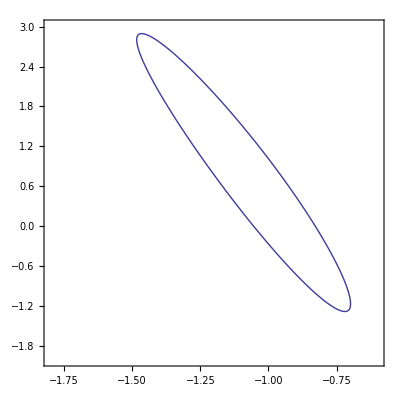

```mathematica
imp1scplw0w1SNomf=ContourPlot[chi2total[{0,0,1},.24,0,.72,w0,w1]==snchi2min[[1]]+2.30,{w0,-1.8,-0.6},{w1,-2,3},DisplayFunction->Identity,PlotPoints->69]
```

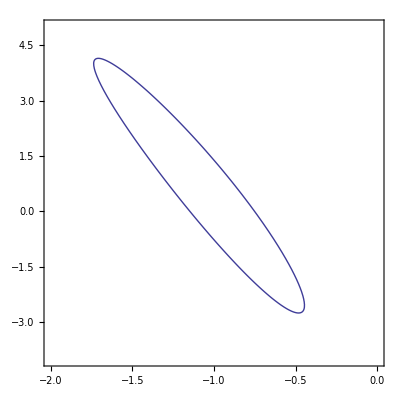

```mathematica
imp2scplw0w1SNomf=ContourPlot[chi2total[{0,0,1},.24,0,.72,w0,w1]==snchi2min[[1]]+6.17,{w0,-2,0},{w1,-4,5},DisplayFunction->Identity,PlotPoints->69]
```

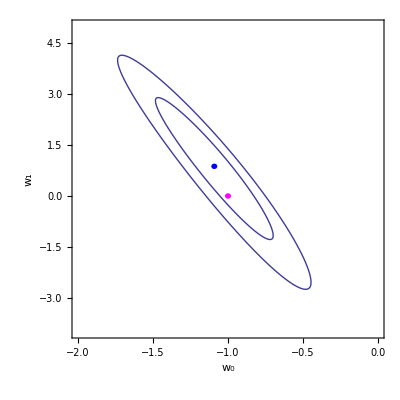

```mathematica
impcplw0w1SNomf=Show[imp1scplw0w1SNomf,imp2scplw0w1SNomf,Graphics[{RGBColor[0,0,1],Disk[{snchi2min[[2,1,2]],snchi2min[[2,2,2]]},{.02,0.08}]}],Graphics[{RGBColor[1,0,1],Disk[{-1,0},{.02,0.08}]}],AspectRatio->1,Frame->True,FrameLabel->{"w_0","w_1"},LabelStyle->{18},ImageSize->{400,400},DisplayFunction->$DisplayFunction,PlotRange->{{-2,0},{-4,5}},Axes->False]
```

```mathematica
Export["Plot_SN_CPL.pdf",impcplw0w1SNomf];
```

## Construction of Contours for CPL parametrisation with BAO+CMB using Ω_m=0.24, Ω_b=0.042

Tasks to perform:
(I) Find the minimum of the χ^2-statistics with the values Ω_m=0.24 and Ω_b=0.042
(II) Find the χ^2-statistics between the priors given for (Ω_m , Ω_b) and ΛCDM
(II) Compute the σ-distance between BAO+CMB and ΛCDM. Tip: Use (I) and (II)
(IV) Compute the contour plot of (I) at 1-2σ of confidence. Tip: You can use around 100 for the plotpoints instructions to perform the task in 1hr and half (more or less). Also include the best fit parameter in this plot.